```mathematica
OS="win";(*or linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
ch=PlanckConstant/(Joule Second);
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\psi-nedm\\Analysis"]];
Print["(ASCII) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];
];
If[OS=="linux",
Print["Working Directory:",curDir=SetDirectory["/home/prajwal/Dropbox/nEDM/psi-nedm/Analysis"]];
Print["(faster) Rawdata Directory:",fastDir="/home/prajwal/nEDM/rawdata"];
Print["(ASCII) Rawdata Directory:",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];
];
Print["Runs in the list: ",runNum={11159,11166,11208,11239,11277,11305,11357,11363,11409,11412,11445,11448}];(*{010119,10124,10135,10166,10189,10191,10207,10246,10270,10273,10281,10345,10386,10391,10417,10420,10463,10471,10497,10541}*)
Print["#Runs in the list: ",runn=Dimensions[runNum][[1]]];
metaStructure={Real,Word,Real,Real,Real,Real,Real};
metaStructure2={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
histbeg=100;histlast=1400;icycle=25;ChNum=1;
chnum={1,2,3,4,5,6,7,8,9,11,12,13,14,15,16,17,18,19};
steps={28,2,2,2,2,20,160,2,2,64,1};(**)
Print["Number of Steps: ",Dimensions[steps][[1]]];
```

Working Directory: C:\Users\Prajwal\Dropbox\nEDM\psi-nedm\Analysis

(ASCII) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

Runs in the list: {11159,11166,11208,11239,11277,11305,11357,11363,11409,11412,11445,11448}

#Runs in the list: 12

Number of Steps: 11

```mathematica
histbeg2=0*(10^9);histlast2=300*(10^9);binw2=1*(10^9);
ptdat2=Table[Table[{0,{0,0}},{k,1,Round[(histlast2-histbeg2)/binw2]}],{l,1,Dimensions[runNum][[1]]}];
For[runi=2,runi≤2(*Dimensions[runNum][[1]]*),runi++,
Clear[data,histdata2];data=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[runi]],10,6],"\\",IntegerString[runNum[[runi]],10,6],"_UCNdet_",IntegerString[icycle,10,3],"_0001.fast.ascii"],metaStructure];
Print["Run#: ",runNum[[runi]],", Size of event list in Cycle-25: ",dimdata=Dimensions[data][[1]]];
histdata2=HistogramList[data[[1;;dimdata,4]],{histbeg2,histlast2,binw2}];
For[i=1,i<=Dimensions[histdata2[[2]]][[1]],i++,
ptdat2[[runi]][[i]][[1]]=(histdata2[[1]][[i]]+((-histdata2[[1]][[1]]+histdata2[[1]][[2]])/2))/(10^9);
ptdat2[[runi]][[i]][[2]][[1]]=histdata2[[2]][[i]];
ptdat2[[runi]][[i]][[2]][[2]]=Sqrt[ptdat2[[runi]][[i]][[2]][[1]]];
];
];
```

{7.22619,35722.1,-0.426891,34.0576}

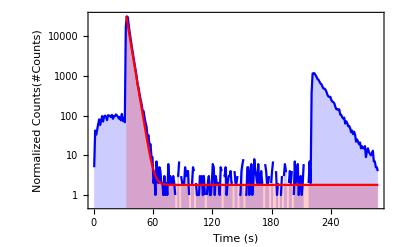

```mathematica
Clear[nlm]
ftdat=Table[Transpose[{ptdat2[[2]][[;;,1]],ptdat2[[2]][[;;,2]][[;;,1]]}][[k]],{k,35,217}];
nlm=NonlinearModelFit[ftdat,{aa+(bb Exp[cc (xx-dd)])},{{aa,1},{bb,30000},{cc,-.3},{dd,33}},xx,Method->NMinimize];
fitparam={aa/.nlm[[1]][[2]],bb/.nlm[[1]][[2]],cc/.nlm[[1]][[2]],dd/.nlm[[1]][[2]]}
fitparamerr=SetPrecision[N[nlm["ParameterErrors"]],10];
ListLogPlot[{Transpose[{ptdat2[[2]][[;;,1]],ptdat2[[2]][[;;,2]][[;;,1]]}],Table[{k,1.8+32000Exp[-.345(k-33)]},{k,33,288}]},PlotStyle->{Blue,Red,Gray},Joined->True,Filling->Axis,PlotRange->Full,Frame->True,PlotRange->Full,FrameLabel->{"Time (s)","Normalized Counts(#Counts)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},PlotLegends->ToString[runNum[[runi-1]]],ImageSize->{1000}]
(*ListLogPlot[{Transpose[{ptdat2[[2]][[;;,1]],ptdat2[[2]][[;;,2]][[;;,1]]}],Table[{k,fitparam[[1]]+fitparam[[2]]Exp[fitparam[[3]](k-fitparam[[4]])]},{k,33,218}]},PlotStyle->{Blue,Red,Gray},Joined->True,Filling->Axis,PlotRange->Full,Frame->True,PlotRange->Full,FrameLabel->{"Time (s)","Normalized Counts(#Counts)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},PlotLegends->ToString[runNum[[runi-1]]],ImageSize->{1000}]*)
```

```mathematica
-Floor[Mean[ptdat2[[2]][[;;,2]][[;;,1]][[;;218]]]*67]+Total[ptdat2[[2]][[;;,2]][[;;,1]][[218-66;;218]]]
```

3

## OLD Code Snippets;

```mathematica
Total[steps[[1;;9]]]
```

220

```mathematica
s=OpenAppend["app.txt"]
WriteString[s,"a"]
Close[s]
```

```mathematica
Clear[write1]
write1=OpenWrite["pslsr_new_0.5T12GeV.dat"]
WriteString[write1,"# N(e)= 10^12, B_wig=0.5T, E_beam=12GeV, Δθ = 20mrad","\n","# E (MeV)" ,"\t |" ,"SRPower (mW/MeV)","|","SLPower (mW/MeV) X 50k","\n"];
For[i=1,i≤g4srsl0ebincn,i++,
WriteString[write1,AccountingForm[SetPrecision[g4psrehist[[i]][[1]],10]],"\t" ,AccountingForm[SetPrecision[g4psrehist[[i]][[2]],10]],"\t",AccountingForm[SetPrecision[g4pslehist[[i]][[2]],10]],"\n"];
];
Close[write1]
```